```mathematica
Integrate[Cosh[kappa*Sin[x]]*Sin[x]/(2*Pi),{x,0,Pi}]
```

1/2 StruveL[-1,kappa]

```mathematica
Integrate[Cosh[kappa*Sin[x]]*1/2*(3*Cos[x]^2-1)*Sin[x],{x,0,Pi}]
```

1-1/2 π StruveL[-1,kappa]+(3 π StruveL[2,kappa])/(2 kappa)

```mathematica
Simplify[(1-1/2 π StruveL[-1,kappa]+(3 π StruveL[2,kappa])/(2 kappa))/(π StruveL[-1,kappa])]
```

-1/2+(1/π+(3 StruveL[2,kappa])/(2 kappa))/StruveL[-1,kappa]

```mathematica
Integrate[Cosh[kappa*Cos[x]]*Sin[x]/(2*Pi),{x,0,Pi}]
```

Sinh[kappa]/(kappa π)

```mathematica
pOnsager[theta_,phi_,kappa_]:=Piecewise[{{Cosh[-kappa*Sin[theta]]/(1/2 StruveL[-1,kappa]),kappa<0},{Cosh[kappa*Cos[theta]]/(Sinh[kappa]/(kappa π)),kappa≥0}}]/(2*Pi)
```

```mathematica
Integrate[Cosh[kappa*Cos[x]]/(Sinh[kappa]/(kappa π))1/2*(3*Cos[x]^2-1)*Sin[x],{x,0,Pi}]
```

(2 π (3+kappa^2-3 kappa Coth[kappa]))/kappa^2

```mathematica
Integrate[Cosh[-kappa*Sin[x]]/(1/2 StruveL[-1,kappa])*Sin[x],{x,0,Pi}]
```

2 π

```mathematica
FullSimplify[Re[ComplexExpand[(+Cosh[kappa] -(1-I)*Sqrt[1/kappa]/Sqrt[2*Pi]+-(1+I)*Sqrt[1/kappa]/Sqrt[2*Pi] Sinh[kappa])/(+Cosh[kappa] (1-I)*Sqrt[1/kappa]*Sqrt[2/Pi]+(1+I)*Sqrt[1/kappa]*Sqrt[2/Pi]* Sinh[kappa])]],Assumptions->kappa >0]
```

1/8 (-2+(2+√kappa √(2 π)-4 Cosh[kappa]) Sech[2 kappa]+√kappa √(2 π) (1+Tanh[2 kappa]))

```mathematica
N[Cosh[500]*Sech[1000]]
```

7.12458×10^-218

```mathematica
1/8 (-2+√kappa √(2 π) (1+Tanh[2 kappa]))
```

```mathematica
Limit[√kappa √(2 π) (1+Tanh[2 kappa]),kappa ->Infinity]
```

∞

```mathematica
Limit[(2+√kappa √(2 π)-4 Cosh[kappa]) Sech[2 kappa],kappa ->Infinity]
```

0

```mathematica
Normal[Series[(3 StruveL[2,kappa])/(2 kappa),{kappa,Infinity,1}]]
```

-1/π+(45 (-1)^(3/4) Cosh[kappa])/(16 kappa^(5/2) √π)+(3 (-1)^(1/4) Cosh[kappa])/(2 kappa^(3/2) √π)-(45 (-1)^(1/4) Sinh[kappa])/(16 kappa^(5/2) √π)-(3 (-1)^(3/4) Sinh[kappa])/(2 kappa^(3/2) √π)

```mathematica
Simplify[ComplexExpand[Re[Normal[Series[-1/2+(1/π+(3 StruveL[2,kappa])/(2 kappa))/StruveL[-1,kappa],{kappa,Infinity,0}]]]],Assumptions->Element[kappa,Reals]&&kappa>0]
```

(-kappa (441+64 kappa^2) Cosh[2 kappa]+15 (9+16 kappa^2) Sinh[2 kappa])/(2 kappa ((9+64 kappa^2) Cosh[2 kappa]-48 kappa Sinh[2 kappa]))

```mathematica
FullSimplify[ComplexExpand[Re[Normal[Series[StruveL[-1,kappa],{kappa,Infinity,1}]]]],Assumptions->Element[kappa,Reals]&&kappa>0]
```

(ⅇ^kappa (-3+8 kappa))/(8 kappa^(3/2) √(2 π))

General::unfl: Underflow occurred in computation.

General::stop: Further output of General::unfl will be suppressed during this calculation.

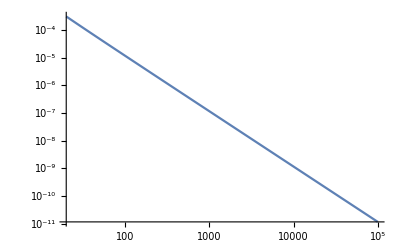

```mathematica
LogLogPlot[((ⅇ^kappa (-3+8 kappa))/(8 kappa^(3/2) √(2 π)))/(StruveL[-1,kappa])-1,{kappa,20,100000}]
```

```mathematica
N[Exp[600]]
```

3.77302×10^260

Power::infy: Infinite expression 1/(0``-0.49714987269413446) encountered.

Power::indet: Indeterminate expression (0``-0.49714987269413446)^0. encountered.

Power::infy: Infinite expression 1/(0``-0.49714987269413446) encountered.

Power::indet: Indeterminate expression (0``-0.49714987269413446)^0. encountered.

Power::infy: Infinite expression 1/(0``-0.49714987269413446) encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Power::indet: Indeterminate expression (0``-0.49714987269413446)^0. encountered.

General::stop: Further output of Power::indet will be suppressed during this calculation.

General::unfl: Underflow occurred in computation.

General::stop: Further output of General::unfl will be suppressed during this calculation.

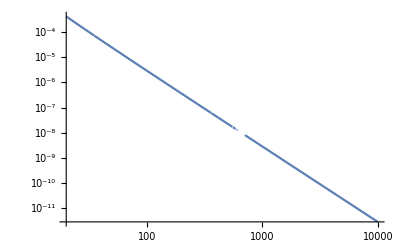

```mathematica
LogLogPlot[((45-27 kappa+8 kappa^2)/(6 kappa-16 kappa^2))/(-1/2+(1/π+(3 StruveL[2,kappa])/(2 kappa))/StruveL[-1,kappa])-1,{kappa,20,10000}]
```

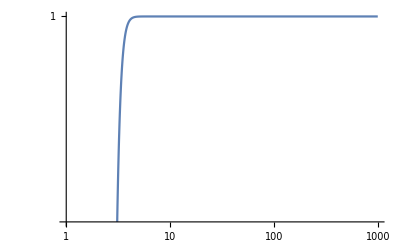

```mathematica
LogLogPlot[Sinh[2*kappa]/Cosh[2*kappa],{kappa,1,1000}]
```

```mathematica
Simplify[(-kappa (441+64 kappa^2) C+15 (9+16 kappa^2) C)/(2 kappa ((9+64 kappa^2)C-48 kappa C))]
```

(45-27 kappa+8 kappa^2)/(6 kappa-16 kappa^2)

```mathematica
pHP[theta_,phi_,phi0_]:=(1/4*(1-Cos[2*phi0]))*(1+Sin[theta]^2*Cos[2*phi0])^(3/2)/(Pi*(1-Sin[theta]^2*Cos[2*phi0]*Cos[2*phi-2*phi0])^2)
```

```mathematica
pHP[theta,phi,phi0]
```

((1-Cos[2 phi0]) (1+Cos[2 phi0] Sin[theta]^2)^(3/2))/(4 π (1-Cos[2 phi-2 phi0] Cos[2 phi0] Sin[theta]^2)^2)

```mathematica
FullSimplify[D[pHP[Pi/2,phi,phi0],phi]]
```

(16 Cos[2 phi0] (1+Cos[2 phi0])^(3/2) Sin[2 phi-2 phi0] Sin[phi0]^2)/(π (-2+Cos[2 phi]+Cos[2 phi-4 phi0])^3)

```mathematica
FullSimplify[Reduce[(16 Cos[2 phi0] (1+Cos[2 phi0])^(3/2) Sin[2 phi-2 phi0] Sin[phi0]^2)/(π (-2+Cos[2 phi]+Cos[2 phi-4 phi0])^3)==0,{phi},Real]]
```

Reduce::bdomv: Warning: Real is not a valid domain specification. Assuming it is a variable to eliminate.

((C[1]|C[2])∈Integers&&phi==π (1/2+C[1])&&(phi0+π C[2]==0||2 phi0+π+2 π C[2]==0))||(C[1]∈Integers&&Cos[2 phi]+Cos[2 (phi-2 phi0)]≠2&&(4 phi0+π==4 π C[1]||phi0==π (1/4+C[1])||2 phi0+π==2 π C[1]||phi0==π (1/2+C[1])||phi0==2 π C[1]||π+2 π C[1]==phi0))||(C[1]∈Integers&&-1/2-phi0/π∉Integers&&Tan[phi0]≠0&&(phi==ArcTan[Tan[phi0]]+π C[1]||phi+ArcTan[Cot[phi0]]==π C[1]))

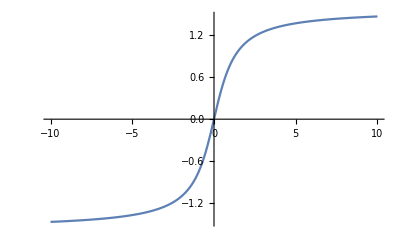

```mathematica
Plot[ArcTan[x],{x,-10,10}]
```

```mathematica
Integrate[pHP[theta,phi,phi0],{phi,0,2*Pi}]
```

$Aborted

```mathematica
Integrate[1-Cos[2*phi0]/(2*(1-Sin[theta]^2*Cos[2*phi0])^(3/2)),{theta,0,Pi}]
```

ConditionalExpression[π-1/4 Cos[2 phi0] Csc[phi0]^2 (EllipticE[Cos[2 phi0]]+√2 EllipticE[1-Csc[phi0]^2/2] √(Sin[phi0]^2)),Re[Cos[2 phi0]]<1]

```mathematica
FullSimplify[π-1/4 Cos[2 phi0] Csc[phi0]^2 (EllipticE[Cos[2 phi0]]+√2 EllipticE[1-Csc[phi0]^2/2] √(Sin[phi0]^2))]
```

π-1/4 Cos[2 phi0] Csc[phi0]^2 (EllipticE[Cos[2 phi0]]+√2 EllipticE[1-Csc[phi0]^2/2] √(Sin[phi0]^2))

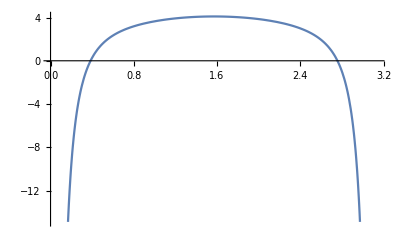

```mathematica
Plot[π-1/4 Cos[2 phi0] Csc[phi0]^2 (EllipticE[Cos[2 phi0]]+√2 EllipticE[1-Csc[phi0]^2/2] √(Sin[phi0]^2)),{phi0,0,Pi}]
```

```mathematica
N[pHP[1,1,ArcTan[8/10]/2]]
```

0.0450382

```mathematica
ArcTan[1]
```

π/4

```mathematica
Cot[Pi/2]
```

0

```mathematica
Assuming[-π/4< P0<π/4,Solve[ArcTan[8/G]/2==P0,G]]
```

{{G→ConditionalExpression[8 Cot[2 P0],(2 Re[P0]==-π/2&&2 Im[P0]<0)||-π/2<2 Re[P0]<π/2||(2 Re[P0]==π/2&&2 Im[P0]>0)]}}

```mathematica
SphericalPlot3D[{1/2*pHP[theta,phi,ArcTan[8/16]/2],pHP[theta,phi,ArcTan[8/8]/2],2*pHP[theta,phi,ArcTan[8/2]/2]},{theta,0,Pi},{phi,0,2*Pi},PlotTheme->"Scientific",PlotRange->All,PlotPoints->300]
```

-Graphics3D-

```mathematica
pOnsager[1,1,3]
```

3/2 Cosh[3 Cos[1]] Csch[3]

```mathematica
SphericalPlot3D[{pOnsager[theta,phi,3]},{theta,0,Pi},{phi,0,2*Pi},PlotRange->All]
SphericalPlot3D[{pOnsager[theta,phi,-3]},{theta,0,Pi},{phi,0,2*Pi},PlotRange->All]
```

-Graphics3D-

-Graphics3D-